```mathematica
Quit[]
```

Declaring Constants All in GeV

```mathematica
Me=.000511;
Mμ=.1057;
Mτ=1.777;
MW=80.4;
Mu= 0.0023;
Md= 0.0048;
Ms = 0.095;
Mc = 1.4;
Mt = 172;
Mb  = 4.2;
MZ=91;
v=246;
Gμ=1.16637*10^-5;
α=1/128;
αs = .1172;
cw =√(1-.23126);
sw = √0.23126;
Bem=-11/3;
Bg=7;
```

This is the function of Rg and Rgamma

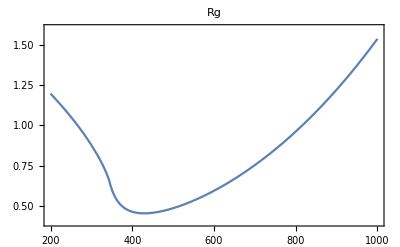

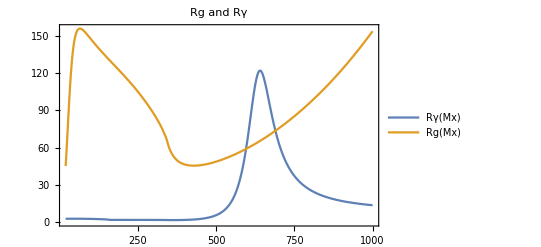

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Tau[M_,Mx_]:= 4 M^2/Mx^2;
ft[τ_]:=Piecewise[{{ArcSin[√(1/τ)]^2, τ≥1}, {-1/4 (Log[(1+√(1-τ))/(1-√(1-τ))]-ⅈ π)^2, τ<1}}]
F1[tau1_]:=2+3tau1+(3tau1)*(2-tau1) ft[tau1];
F12[tau12_]:= -2tau12(1+(1-tau12) ft[tau12]);
SumLoopCorrectionRγ[Mx_]:=       F12[Tau[Me,Mx]]+F12[Tau[Mμ,Mx]]+F12[Tau[Mτ,Mx]]+F1[Tau[MW,Mx]] + 3(2/3)^2 F12[Tau[Mu,Mx]]+3(-1/3)^2 F12[Tau[Md,Mx]]+ 3(2/3)^2 F12[Tau[Mc,Mx]]+3(-1/3)^2 F12[Tau[Ms,Mx]]+ 3(2/3)^2 F12[Tau[Mt,Mx]]+3(-1/3)^2 F12[Tau[Mb,Mx]];
SumLoopCorrectionRg[Mx_]:=F12[Tau[Mu,Mx]]+F12[Tau[Md,Mx]]+F12[Tau[Ms,Mx]]+F12[Tau[Mc,Mx]]+F12[Tau[Mt,Mx]]+F12[Tau[Mb,Mx]];
Rg[Mx_]:=Abs[-Bg+1/2 SumLoopCorrectionRg[Mx]]^2/Abs[1/2 SumLoopCorrectionRg[Mx]]^2;
Rγ[Mx_]:=Abs[-Bem+SumLoopCorrectionRγ[Mx]]^2/Abs[SumLoopCorrectionRγ[Mx]]^2
Plot[{Rγ[Mx],Rg[Mx]},{Mx,20,1000},PlotLegends->"Expressions",Frame->True, AxesOrigin->{20,0},PlotLabel->"Rg and Rγ",Exclusions-> None]
Plot[Rg[Mx]/100,{Mx,200,1000},PlotRange ->{{200,1000},{.4,1.6}},PlotLegends->"Expressions",Frame->True, AxesOrigin->{20,0},PlotLabel ->"Rg",Exclusions-> None]
```

Higgs Gamma Gamma and Higgs Gluon Gluon decay

```mathematica
TauH[M_,Mh_]:= Mh^2/(4 M^2);
ftH[τ_]:=Piecewise[{{ArcSin[√τ]^2, τ≤1}, {-1/4(Log[(1+√(1-τ^-1))/(1-√(1-τ^-1))]-ⅈ*π)^2, τ>1}}]
A12H[tauHi_]:=2(tauHi+(tauHi-1)*ftH[tauHi])*(tauHi)^-2
A1H[tauHi_]:=-(2(tauHi)^2+3tauHi+3(2tauHi-1)*ftH[tauHi])tauHi^-2;
SumFermionsAndWHiggs[Mh_]:=A12H[TauH[Me,Mh]]+A12H[TauH[Mμ,Mh]]+A12H[TauH[Mτ,Mh]]+A1H[TauH[MW,Mh]] + 3(2/3)^2 A12H[TauH[Mu,Mh]]+3(-1/3)^2 A12H[TauH[Md,Mh]]+ 3(2/3)^2 A12H[TauH[Mc,Mh]]+3(-1/3)^2 A12H[TauH[Ms,Mh]]+ 3(2/3)^2*A12H[TauH[Mt,Mh]]+3(-1/3)^2 A12H[TauH[Mb,Mh]];
WidthHγγ[Mh_]:=(Gμ α^2 Mh^3)/(128 √2 π^3)Abs[SumFermionsAndWHiggs[Mh]]^2;
LogLogPlot[Re[WidthHγγ[Mh]]*1000000,{Mh,100,1000},PlotRange ->{{100,1000},{1,150}}PlotLegends->"Expressions",AxesLabel -> {Hx,WidthHγγ},AxesOrigin->{100,0},PlotLabel ->"Width of Higgs Gamma Gamma Decay",Exclusions-> None,MaxRecursion->5]
SumQuarks[Mh_]:=A12H[TauH[Mb,Mh]]+A12H[TauH[Mt,Mh]];
WidthHgg[Mh_]:= (Gμ αs^2 Mh^3)/(36 √2 π^3)Abs[(3/4)* SumQuarks[Mh]]^2
LogLogPlot[WidthHgg[Mh]*1000,{Mh,100,1000},PlotLegends->"Expressions",AxesLabel -> {Mh,WidthHgg},AxesOrigin->{100,0},PlotLabel ->"Width of Higgs Gluon Gluon Decay" ,Exclusions->None,MaxRecursion->5]
```

WIdth of the Dilaton for GG and gamma gamma

```mathematica
WidthXγγ[Mx_,f_]:=Rγ[Mx](v^2/f^2) WidthHγγ[Mx];
Plot3D[WidthXγγ[Mx,f],{f,500,4500},{Mx,20,1000}, ColorFunction->"TemperatureMap",PlotLabel-> "Width of the Dilaton Gamma Gamma Decay",AxesLabel->{"f(GeV)","Mx (GeV)","Γ(X->γγ)(GeV)"},ClippingStyle->Red,Exclusions->None,MaxRecursion->5]
WidthXgg[Mx_,f_]:= Rg[Mx](v^2/f^2) WidthHgg[Mx];
Plot3D[WidthXgg[Mx,f],{f,500,4500},{Mx,20,1000}, ColorFunction->"TemperatureMap",PlotLabel-> "Width of the Dilaton Gluon Gluon Decay",AxesLabel->{"f(GeV)","Mx(GeV)","Γ(X->γγ)(GeV)"},Exclusions-> None,MaxRecursion->5]
```

This section is for the Higgs Decay into ZZ and WW for two body decay

```mathematica
xZ[Mh_]:=MZ^2/Mh^2;
xW[Mh_]:=MW^2/Mh^2;
WidthHZZ[Mh_]:=(Gμ Mh^3)/(16 √2 π)1 √(1-4xZ[Mh])(1-4xZ[Mh]+12 xZ[Mh]^2);
WidthHWW[Mh_]:=(Gμ Mh^3)/(16 √2 π)2 √(1-4xW[Mh])(1-4xW[Mh]+12 xW[Mh]^2);
LogLogPlot[WidthHZZ[Mh],{Mh,20,200}]
LogLogPlot[WidthHWW[Mh],{Mh,20,200}]
```

Three Body Decays involving Vector Bosons

```mathematica
δW=1;
δZ=7/12-(10/9)sw^2+40/9 sw^4;
Rt[x_]:=(3(1-8x+20 x^2))/(√(4x-1))ArcCos[(3x-1)/(2 x^(3/2))]-((1-x)/(2x))(2-13x+47 x^2)-3/2(1-6x+4 x^2)Log[x];
WidthHZZ3body[Mh_]:=(3 Gμ^2 MZ^4)/(16 π^3)Mh δZ Rt[xZ[Mh]];
WidthHWW3body[Mh_]:=(3 Gμ^2 MW^4)/(16 π^3)Mh δZ Rt[xW[Mh]];
Plot[Re[WidthHZZ3body[Mh]],{Mh,20,200},Exclusions->None]
Plot[Re[WidthHWW3body[Mh]],{Mh,20,200},Exclusions->None]
```

The combined widths of three body and two body

```mathematica
TotalWidthHZZ[Mh_]:=Piecewise[{{WidthHZZ3body[Mh],Mh<2*MZ},{WidthHZZ[Mh],Mh>2*MZ}}];
TotalWidthHWW[Mh_]:=Piecewise[{{WidthHWW3body[Mh],Mh<2*MW},{WidthHWW[Mh],Mh>2*MW}}];
Plot[Re[TotalWidthHZZ[Mh]],{Mh,20,200}]
Plot[Re[TotalWidthHWW[Mh]],{Mh,20,200}]
```

This is for the decay width of a Higgs to a photon and a Z Note the use of the Taus from the dilaton calculations

```mathematica
λ[M_]:=4 M^2/MZ^2
vfu=2(1/2)^3-4(2/3)sw^2;
vfd=2(-1/2)^3-4(-1/3)sw^2;
vfc=2(1/2)^3-4(2/3)sw^2;
vfs=2(-1/2)^3-4(-1/3)sw^2;
vft=2(1/2)^3-4(2/3)sw^2;
vfb=2(-1/2)^3-4(-1/3)sw^2;
vfe=2(-1/2)^3-4(-3/3)sw^2;
vfμ=2(-1/2)^3-4(-3/3)sw^2;
vfτ=2(-1/2)^3-4(-3/3)sw^2;
g[τ_]=Piecewise[{{√(τ^-1-1)ArcSin[√τ], τ≥1}, {(√(1-τ^-1))/2 (Log[(1+√(1-τ^-1))/(1-√(1-τ^-1))]-ⅈ π), τ<1}}];
fZγ[τ_]:=Piecewise[{{ArcSin[√τ]^2, τ≥1}, {-1/4(Log[(1+√(1-(τ^-1)))/(1-√(1-(τ^-1)))]-ⅈ*π)^2, τ<1}}];
I1[τ_,λ_]:=(τ λ)/(2(τ-λ))+(τ^2 λ^2)/(2(τ-λ)^2)(fZγ[τ^-1]-fZγ[λ^-1])+(τ^2 λ)/(τ-λ)^2(g[τ^-1]-g[λ^-1]);
I2[τ_,λ_]:=(-τ λ)/(2(τ-λ))(fZγ[τ^-1]-fZγ[λ^-1]);
A12HZγ[τ_,λ_]:=(I1[τ,λ]-I2[τ,λ]);
A1HZγ[τ_,λ_]:=cw(4(3-sw^2/cw^2)I2[τ,λ]+((1+2/τ)sw^2/cw^2-(5+2/τ))I1[τ,λ]);
FermionLoop[Mh_] := (- vfe)/cw A12HZγ[Tau[Me,Mh],λ[Me]]+ (- vfμ)/cw A12HZγ[Tau[Mμ,Mh],λ[Mμ]]+ (- vfτ)/cw A12HZγ[Tau[Mτ,Mh],λ[Mτ]]+ 3((2/3)vfu)/cw A12HZγ[Tau[Mu,Mh],λ[Mu]]+3((-1/3)vfd)/cw A12HZγ[Tau[Md,Mh],λ[Md]]+3((2/3)vfc)/cw A12HZγ[Tau[Mc,Mh],λ[Mc]]+3((-1/3)vfs)/cw A12HZγ[Tau[Ms,Mh],λ[Ms]]+ 3((2/3)vft)/cw A12HZγ[Tau[Mt,Mh],λ[Mt]]+3((-1/3)vfb)/cw A12HZγ[Tau[Mb,Mh],λ[Mb]];
WidthHZγ[Mh_]:=(Gμ^2 MW^2 α Mh^3)/(64 π^4)(1-MZ^2/Mh^2)^3 Abs[A1HZγ[Tau[MW,Mh],λ[MW]]]^2;
LogLogPlot[WidthHZγ[Mh]*1000000,{Mh,100,1000},AspectRatio->1]
```

Top Quark Decays for the Higgs Boson With full QCD corrections

Note the use of the top quark  mass of 178 ans the strong coupling constant at .1172

```mathematica
βt[Mh_]:=(1-4 178^2/Mh^2)^(1/2);
Atop[β_]:=(1-β^2)(4PolyLog[2,(1-β)/(1+β)]+2PolyLog[2,-(1-β)/(1+β)]-3Log[(1+β)/(1-β)]Log[2/(1+β)]-2Log[(1+β)/(1-β)]Log[β])-3β Log[4/(1-β^2)]-4β Log[β];
ΔtH[β_]:=1/β Atop[β]+1/(16 β^3)(3+34 β^2-13 β^4)Log[(1+β)/(1-β)]+3/(8 β^2)(7 β^2-1);
WidthHTT[Mh_]:=(3Gμ)/(4 √2 π) Mh 178^2 βt[Mh]^3(1+4/3 (.1172)/π ΔtH[βt[Mh]]);
LogPlot[Re[WidthHTT[Mh]],{Mh,350,700},AspectRatio->1,Frame -> True,PlotRange->{{350,700},{1,50}}]
```

Born approximation for fermion decays

```mathematica
β[M_,Mh_]:=(1-4 M^2/Mh^2)^(1/2);
WidthHeeBorn[Mh_]:=Gμ/(4 √2 π)Mh Me^2 β[Me,Mh]^3;
WidthHμμBorn[Mh_]:=Gμ/(4 √2 π)Mh Mμ^2 β[Mμ,Mh]^3;
WidthHττBorn[Mh_]:=Gμ/(4 √2 π)Mh Mτ^2 β[Mτ,Mh]^3;
WidthHuuBorn[Mh_]:=Gμ/(4 √2 π)Mh Mu^2 β[Mu,Mh]^3;
WidthHddBorn[Mh_]:=Gμ/(4 √2 π)Mh Md^2 β[Md,Mh]^3;
WidthHssBorn[Mh_]:=Gμ/(4 √2 π)Mh Ms^2 β[Ms,Mh]^3;
WidthHccBorn[Mh_]:=Gμ/(4 √2 π)Mh Mc^2 β[Mc,Mh]^3;
WidthHbbBorn[Mh_]:=Gμ/(4 √2 π)Mh Mb^2 β[Mb,Mh]^3;
WidthHttBorn[Mh_]:=Gμ/(4 √2 π)Mh Mt^2 β[Mt,Mh]^3;
```

Total Width of the Higgs Boson

```mathematica
TotalWidthHiggs[Mh_] :=Re[WidthHuuBorn[Mh]+WidthHddBorn[Mh]+WidthHccBorn[Mh]+WidthHssBorn[Mh]+WidthHbbBorn[Mh]+WidthHττBorn[Mh]+WidthHμμBorn[Mh]+WidthHeeBorn[Mh]+ WidthHttBorn[Mh]+WidthHZγ[Mh]+TotalWidthHZZ[Mh]+TotalWidthHWW[Mh]+WidthHgg[Mh]+WidthHγγ[Mh]];
LogLogPlot[Re[TotalWidthHiggs[Mh]],{Mh,100,1000}]
TotalTreeWidth[Mh_]:=Re[WidthHuuBorn[Mh]+WidthHddBorn[Mh]+WidthHccBorn[Mh]+WidthHssBorn[Mh]+WidthHbbBorn[Mh]+WidthHττBorn[Mh]+WidthHμμBorn[Mh]+WidthHeeBorn[Mh]+ WidthHttBorn[Mh]+TotalWidthHZZ[Mh]+TotalWidthHWW[Mh]];
LogLogPlot[Re[TotalTreeWidth[Mh]],{Mh,20,1000}]
```

BBbar branching ratios

```mathematica
BranchingRatioBBbar[Mh_]:=WidthHbbBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioBBbar[Mh]],{Mh,100,1000}]
```

ττ Branching ratio

```mathematica
BranchingRatioττ[Mh_]:=WidthHττBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioττ[Mh]],{Mh,100,1000}]
```

gg branching ratio

```mathematica
BranchingRatiogg[Mh_]:=WidthHgg[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatiogg[Mh]],{Mh,100,1000}]
```

CCbar branching ratio

```mathematica
BranchingRatioCCbar[Mh_]:=WidthHccBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioCCbar[Mh]],{Mh,100,1000}]
```

γγ branching ratio

```mathematica
BranchingRatioγγ[Mh_]:=WidthHγγ[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioγγ[Mh]],{Mh,100,1000}]
```

Ssbar branching ratio

```mathematica
BranchingRatioSSbar[Mh_]:=WidthHssBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioSSbar[Mh]],{Mh,100,1000}]
```

μμ branching ratio

```mathematica
BranchingRatioμμ[Mh_]:=WidthHμμBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioμμ[Mh]],{Mh,100,1000}]
```

Zγ branching ratio

```mathematica
BranchingRatioZγ[Mh_]:=WidthHZγ[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioZγ[Mh]],{Mh,100,1000}]
```

WW branching ratio

```mathematica
BranchingRatioWW[Mh_]:=TotalWidthHWW[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioWW[Mh]],{Mh,100,1000}]
```

ZZ Branching ratio

```mathematica
BranchingRatioZZ[Mh_]:=TotalWidthHZZ[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioZZ[Mh]],{Mh,100,1000}]
```

TTbar Branching Ratio

```mathematica
BranchingRatioTTbar[Mh_]:=WidthHttBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioTTbar[Mh]],{Mh,100,1000}]
```

This is the cross section of production and decay of the Dilaton over the same for the Higgs

```mathematica
TotalWidthHiggs[200]
Rg[200]
Rγ[200]
WidthXγγ[200,4000]
WidthXgg[200,4000]
TotalTreeWidth[200]
```

```mathematica
σggXγγOVERσggHγγ[f_,Mx_] := v^2/f^2 Rg[Mx]Rγ[Mx](TotalWidthHiggs[Mx])/(TotalTreeWidth[Mx]+f^2/v^2 WidthXγγ[Mx,f]+f^2/v^2 WidthXgg[Mx,f]) ;
σggXγγOVERσggHγγ[2000,100]
ContourPlot[σggXγγOVERσggHγγ[f,Mx],{Mx,20,200},{f,500,4500},Contours->{.1,.2,.5,1,2,5,10},ContourShading->False,ContourLabels->True,PlotPoints->50,AspectRatio->1/GoldenRatio,ImageSize->Large]
Plot3D[σggXγγOVERσggHγγ[f,Mx],{Mx,20,1000},{f,500,4500}]
```

Interpolated production function gg fusion

```mathematica
ggHiggs=Interpolation[{{10.,6996.},{15.,4275.},{20.,2085.},{25.,1146.},{30.,710.3},{35.,484.6},{40.,355.5},{45.,275.1},{50.,221.4},{55.,183.5},{60.,155.5},{65.,134.1},{70.,117.2},{75.,103.6},{80.,92.4},{85.,83.02},{90.,75.07},{95.,68.25},{100.,62.35},{105.,57.2},{110.,52.68},{115.,48.69},{120.,45.14},{125.,41.98},{130.,39.14},{135.,36.59},{140.,34.28},{145.,32.19},{150.,30.29},{160.,26.97},{170.,24.19},{180.,21.84},{190.,19.84},{200.,18.12},{210.,16.65},{220.,15.37},{230.,14.26},{240.,13.31},{250.,12.48},{260.,11.76},{270.,11.14},{280.,10.62},{290.,10.18},{300.,9.823},{310.,9.559},{320.,9.392},{330.,9.349},{340.,9.521},{350.,10.25},{360.,10.63},{370.,10.64},{380.,10.4},{390.,10.},{400.,9.516},{410.,8.976},{420.,8.415},{430.,7.853},{440.,7.301},{450.,6.771},{460.,6.266},{470.,5.788},{480.,5.341},{490.,4.924},{500.,4.538},{550.,3.008},{600.,2.006},{650.,1.352},{700.,0.9235},{750.,0.6398},{800.,0.4491},{850.,0.3195},{900.,0.2301},{950.,0.1675},{1000.,0.1233},{1050.,0.09159},{1100.,0.06868},{1150.,0.05193},{1200.,0.03958},{1250.,0.0304},{1300.,0.02349},{1350.,0.01828},{1400.,0.01431},{1450.,0.01126},{1500.,0.008913},{1550.,0.007089},{1600.,0.005666},{1650.,0.004546},{1700.,0.003662},{1750.,0.002965},{1800.,0.002408},{1850.,0.001963},{1900.,0.001606},{1950.,0.001317},{2000.,0.001084},{2050.,0.0008953},{2100.,0.0007415},{2150.,0.0006144},{2200.,0.0005108},{2250.,0.0004267},{2300.,0.0003569},{2350.,0.0002988},{2400.,0.0002509},{2450.,0.000211},{2500.,0.0001778},{2550.,0.0001499},{2600.,0.0001272},{2650.,0.0001077},{2700.,0.00009121},{2750.,0.00007771},{2800.,0.00006611},{2850.,0.00005636},{2900.,0.00004809},{2950.,0.00004112},{3000.,0.00003502}}]
LogPlot[ggHiggs[M],{M,10,3000}]
ggHiggs[201]
```

The interpolated sigma of the background events diphoton

InterpolatingFunction[{{253.192, 1608.3}}, <>]

InterpolatingFunction::dmval: Input value {20.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

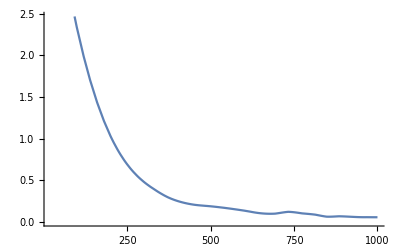

```mathematica
backgroundsigmaγγ=Interpolation[{{253.1916175,26.9004837},{292.4307133,20.20630914},{331.0752772,15.61955991},{372.3340943,11.77642715},{411.117804,9.545397047},{453.1440309,8.181588189},{495.5834784,7.561937921},{531.3860963,6.941926235},{613.7561516,5.082614012},{653.4422003,4.09070374},{693.3938908,3.966918253},{732.6034708,4.835043039},{774.1700951,4.091065158},{813.7338642,3.471053472},{847.8511773,2.509740504},{884.6427019,2.696016963},{926.5405121,2.412205668},{967.5765966,2.26224439},{1047.281422,2.241281644},{1088.154131,2.219860012},{1166.830652,2.435976278},{1405.961147,2.290344562},{1568.446102,2.219860012},{1608.300117,2.219860012}}]
Plot[backgroundγγ[Mx]/40,{Mx,20,1000}]
```

The interpolated background event number

```mathematica
DiphotonEventNumber=Interpolation[{{168.2282681,3746.862118},{203.2290689,1575.767587},{238.1978354,738.479694},{287.4411368,385.6620421},{332.6032538,197.0928395},{367.475917,127.8153672},{416.6807771,76.01122697},{455.6346246,50.3725988},{541.7110953,22.60642952},{619.5290941,13.44394248},{715.7925085,6.723357536},{820.2118848,3.5880537},{926.6494291,2.088090013},{1045.381782,1.090479624},{1116.997918,0.822925465},{1221.359632,0.533669923},{1362.541702,0.310572508},{1415.750864,0.24474551},{1554.876324,0.148735211},{1687.819143,0.107485025},{147.6621742,5777.706625},{176.4995538,2707.708329},{190.8958195,1999.587618},{219.6691303,1163.672366},{231.9895659,957.6156226},{256.6368442,634.6113527},{268.9893142,468.6475975},{303.8811981,284.8035868},{355.1554813,155.3182793},{394.1285495,96.45528283},{439.2265977,61.21161751},{498.6760634,33.38189385},{529.3970666,26.88234093},{570.3690822,19.42679932},{601.1221198,14.03897573},{644.1187104,10.82636734},{674.8397135,8.718441774},{693.2787223,7.492179098},{734.2315173,5.777706625},{762.8830973,5.073751043},{793.6041004,4.085876791},{850.9200741,3.017337043},{881.6346704,2.483043489},{904.1420497,2.277019612},{951.2262316,1.75595793},{977.834016,1.542012074},{1006.49841,1.296739275},{1031.049585,1.189145809},{1071.976752,1},{1145.655905,0.707179692},{1176.35128,0.621016942},{1196.814864,0.569489726},{1252.061415,0.458608401},{1282.750383,0.41154759},{1319.577146,0.361404645},{1393.237078,0.272732364},{1444.38963,0.224438408},{1475.078599,0.201407313},{1499.61696,0.192870789},{1532.349724,0.173079055},{1595.771457,0.139380054},{1644.873807,0.11721023},{1726.689701,0.094389053}},InterpolationOrder->1]
InterpolatingFunction[{{147.662, 1726.69}}, <>]
```

InterpolatingFunction::dmval: Input value {10.0202} lies outside the range of data in the interpolating function. Extrapolation will be used.

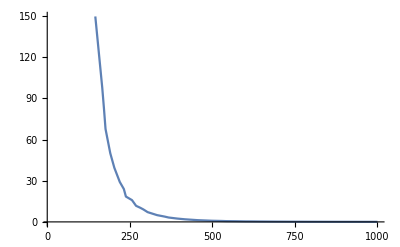

```mathematica
Plot[DiphotonEventNumber[Mx]/40,{Mx,10,1000}]
```

New 3d stuff for Jacob. This is the cross section of dilaton on mf plane

```mathematica
σggXγγ[Mx_,f_]:=σggXγγOVERσggHγγ[f,Mx]*ggHiggs[Mx]*BranchingRatioγγ[Mx];
Plot3D[σggXγγ[Mx,f],{Mx,100,300},{f,500,4500},Exclusions->None]
```

-Graphics3D-

Exclusion Plane

```mathematica
DiscoveryThreshold[Mx_,f_]=5 (backgroundsigmaγγ[Mx]/40)/(σggXγγOVERσggHγγ[f,Mx]*ggHiggs[Mx]*BranchingRatioγγ[Mx] 1000);
Plot3D[DiscoveryThreshold[Mx,f],{Mx,100,1000},{f,20,4500},PlotRange->{0,10}]
```

InterpolatingFunction::dmval: Input value {100.064} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

Current luminosity detection threshold

```mathematica
currentdetection[Mx_,f_]=3200σggXγγ[Mx,f] 1/(√backgroundsigmaγγ[Mx]);
Plot3D[currentdetection[Mx,f],{Mx,20,1000},{f,500,4500},PlotRange->{0,5}]
```

InterpolatingFunction::dmval: Input value {20.0701} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

Here is where I will try interpolating things

```mathematica
TotalWidthHiggsInterpolated =FunctionInterpolation[Re[TotalWidthHiggs[Mx]],{Mx,20,1000}]
LogLogPlot[TotalWidthHiggsInterpolated[Mx],{Mx,20,1000}]
TotalTreeWidthInterpolated=FunctionInterpolation[Re[TotalTreeWidth[Mx]],{Mx,20,1000}]
LogLogPlot[TotalWidthHiggsInterpolated[Mx],{Mx,20,1000}]
```

Here is where I try to make the 3D interpolations

```mathematica
WidthXγγInterpolated=FunctionInterpolation[Re[WidthXγγ[Mx,f]],{Mx,20,1000},{f,500,4500}]
Plot3D[WidthXγγInterpolated[Mx,f],{Mx,20,1000},{f,500,4500}]
WidthXggInterpolated=FunctionInterpolation[Re[WidthXgg[Mx,f]],{Mx,20,1000},{f,500,4500}]
Plot3D[WidthXggInterpolated[Mx,f],{Mx,20,1000},{f,500,4500}]
```

This is the cross section ratio with interpolated functions

```mathematica
σggXγγOVERσggHγγInterpolated[f_,Mx_] = v^2/f^2 Rg[Mx]Rγ[Mx]((TotalWidthHiggsInterpolated[Mx])/(TotalTreeWidthInterpolated[Mx]*f^2/v^2 WidthXggInterpolated[Mx,f]+f^2/v^2*WidthXγγInterpolated[Mx,f] ));
σggXγγOVERσggHγγInterpolated[4000,200]
ContourPlot[σggXγγOVERσggHγγInterpolated[f,Mx],{Mx,20,200},{f,500,4500},Contours->{10,5,2,1,0.5,0.2,0.1},PlotLegends->{"10","5","2","1","0.5","0.2","0.1"}]
Plot3D[σggXγγOVERσggHγγInterpolated[f,Mx],{Mx,20,1000},{f,500,4500}]
```